# LeafComplexity

Compute a sum or other complexity measure over all atoms of an expression

## Definition

### Identity scaling

#### All nodes

```mathematica
(*use of global symbols and redundant function definitions aims at improving efficiency of interpreted code*)
```

```mathematica
ClearAll[lt]

lt[e:_Integer|_Real]:=AddTo[s,Abs@e];
lt[e_Symbol]:=If[NumericQ[e],AddTo[s,Abs@e],Increment[s]];
lt[e_DirectedInfinity]:=AddTo[s,Infinity]
lt[e_]:=Increment[s]

lt[e_Complex]:=Scan[lt[#]&,ReIm[e],Heads->True];
lt[e_Rational]:=Scan[lt[#]&,NumeratorDenominator[e],Heads->True]			
lt[e_Association]:=Scan[lt[#]&,Values[e],Heads->True]		
	
lt[e_]/;!AtomQ[e]:=Scan[lt,e,Heads->True]
```

```mathematica
leafTotal[expr_]:=Block[{s=1(*see important definition detail*)},lt[expr];s]
```

#### Proper leaf nodes

```mathematica
ClearAll[plt]

plt[e:_Integer|_Real]:=AddTo[s,Abs@e];
plt[e_Symbol]:=If[NumericQ[e],AddTo[s,Abs@e],Increment[s]];
plt[e_DirectedInfinity]:=AddTo[s,Infinity]
plt[e_]:=Increment[s]

plt[e_Complex]:=Scan[plt[#]&,ReIm[e],Heads->False];
plt[e_Rational]:=Scan[plt[#]&,NumeratorDenominator[e],Heads->False]			
plt[e_Association]:=Scan[plt[#]&,Values[e],Heads->False]		
	
plt[e_]/;!AtomQ[e]:=Scan[plt,e,Heads->False]
```

```mathematica
properLeafTotal[expr_]:=Block[{s=1},plt[expr];s]
```

### Custom scaling

#### All nodes

```mathematica
ClearAll[slt]

slt[e:_Integer|_Real,f_]:=AddTo[s,f[e]];
slt[e_Symbol,f_]:=If[NumericQ[e],AddTo[s,f[e]],AddTo[s,f[1]]];
slt[e_DirectedInfinity,f_]:=AddTo[s,f[e]]
slt[e_,f_]:=AddTo[s,f[1]]

slt[e_Complex,f_]:=Scan[slt[#,f]&,ReIm[e],Heads->True];
slt[e_Rational,f_]:=Scan[slt[#,f]&,NumeratorDenominator[e],Heads->True]			
slt[e_Association,f_]:=Scan[slt[#,f]&,Values[e],Heads->True]		
	
slt[e_,f_]/;!AtomQ[e]:=Scan[slt[#,f]&,e,Heads->True]
```

```mathematica
scalingLeafTotal[expr_,f_]:=Block[{s=1},slt[expr,f];s]
```

#### Proper leaf nodes

```mathematica
ClearAll[splt]

splt[e:_Integer|_Real,f_]:=AddTo[s,f[e]];
splt[e_Symbol,f_]:=If[NumericQ[e],AddTo[s,f[e]],AddTo[s,f[1]]];
splt[e_DirectedInfinity,f_]:=AddTo[s,f[e]]
splt[e_,f_]:=AddTo[s,f[1]]

splt[e_Complex,f_]:=Scan[splt[#,f]&,ReIm[e],Heads->False];
splt[e_Rational,f_]:=Scan[splt[#,f]&,NumeratorDenominator[e],Heads->False]			
splt[e_Association,f_]:=Scan[splt[#,f]&,Values[e],Heads->False]		
	
splt[e_,f_]/;!AtomQ[e]:=Scan[splt[#,f]&,e,Heads->False]
```

```mathematica
scalingProperLeafTotal[expr_,f_]:=Block[{s=1},splt[expr,f];s]
```

### Custom wrapping

#### All nodes

```mathematica
ClearAll[wlt]

wlt[e:_Integer|_Real,f_,g_]:=s=g[s,f[e]];
wlt[e_Symbol,f_,g_]:=If[NumericQ[e],s=g[s,f[e]],s=g[s,f[1]]];
wlt[e_DirectedInfinity,f_,g_]:=s=g[s,f[e]]
wlt[e_,f_,g_]:=s=g[s,f[1]]

wlt[e_Complex,f_,g_]:=Scan[wlt[#,f,g]&,ReIm[e],Heads->True];
wlt[e_Rational,f_,g_]:=Scan[wlt[#,f,g]&,NumeratorDenominator[e],Heads->True]			
wlt[e_Association,f_,g_]:=Scan[wlt[#,f,g]&,Values[e],Heads->True]		
	
wlt[e_,f_,g_]/;!AtomQ[e]:=Scan[wlt[#,f,g]&,e,Heads->True]
```

```mathematica
wrappingLeafTotal[expr_,f_,g_]:=Block[{s=1},wlt[expr,f,g];s]
```

#### Proper leaf nodes

```mathematica
ClearAll[pwlt]

pwlt[e:_Integer|_Real,f_,g_]:=s=g[s,f[e]];
pwlt[e_Symbol,f_,g_]:=If[NumericQ[e],s=g[s,f[e]],s=g[s,f[1]]];
pwlt[e_DirectedInfinity,f_,g_]:=s=g[s,f[e]]
pwlt[e_,f_,g_]:=s=g[s,f[1]]

pwlt[e_Complex,f_,g_]:=Scan[pwlt[#,f,g]&,ReIm[e],Heads->False];
pwlt[e_Rational,f_,g_]:=Scan[pwlt[#,f,g]&,NumeratorDenominator[e],Heads->False]			
pwlt[e_Association,f_,g_]:=Scan[pwlt[#,f,g]&,Values[e],Heads->False]		
	
pwlt[e_,f_,g_]/;!AtomQ[e]:=Scan[pwlt[#,f,g]&,e,Heads->False]
```

```mathematica
wrappingProperLeafTotal[expr_,f_,g_]:=Block[{s=1},pwlt[expr,f,g];s]
```

### Main

```mathematica
ClearAll[LeafComplexity]

Options[LeafComplexity]={Heads->True};

LeafComplexity[expr_,opt:OptionsPattern[LeafComplexity]]:=
	If[OptionValue[Heads],
				leafTotal[expr],
				properLeafTotal[expr]]

LeafComplexity[expr_,f:_Function|_Symbol,opt:OptionsPattern[LeafComplexity]]:=
	If[OptionValue[Heads],
				scalingLeafTotal[expr,f],
				scalingProperLeafTotal[expr,f]]

LeafComplexity[expr_,f:_Function|_Symbol,g:_Function|_Symbol,opt:OptionsPattern[LeafComplexity]]:=
	If[OptionValue[Heads],
				wrappingLeafTotal[expr,f,g],
				wrappingProperLeafTotal[expr,f,g]]
```

## Documentation

### Usage

LeafComplexity[expr]

gives the sum of all the numeric indivisible subexpressions in expr.

LeafComplexity[expr, f]

apply a function f to each indivisible subexpression in expr and take the Total.

LeafComplexity[expr, f, g]

apply a function f to each indivisible subexpression in expr and Apply to it recursively another unary or binary function g.

### Details & Options

Any Wolfram Language expression can be broken down as a TreeForm. An expression's LeafCount gives its total number of indivisible subexpressions or leaves.

LeafComplexity directly extends LeafCount by weighing each leaf by its absolute numeric value and then taking their sum. If a leaf is non-numeric, it is counted by default as 1. Even if already atoms, expressions with Rational, Complex or Association heads are decomposed into their subparts.

LeafComplexity also accepts as second argument a custom Function f to be applied to all leaves before taking their Total. Even more generally, a third argument can be specified to recursively Apply to each function-of-the-leaf another unary or binary function g. Setting this to Plus recovers the other definitions UpTo two arguments.

LeafComplexity accepts the following options:

Heads | True | consider also the subexpression heads as leaves

LeafComplexity can work as a measure of complexity for algebraic expressions.

An important detail in the definition and design of LeafComplexity is the following. Since in the most general usage case one may sometimes want to choose as third argument Times instead of the default Plus, then in order to avoid returning identically null results, all LeafComplexity usage definitions are implemented as recursions starting from initial condition 1 instead of 0. This in practice induces the somewhat akward "correspondence principle" that if all leaves are equal 1 or -1, LeafComplexity[expr]=LeafCount[expr]+1. One may desire to see complete equality with LeafCount in this special case, but a better trade-off seems to maintain the internal consistency and generality of LeafComplexity itself.

## Examples

### Basic Examples

Expressions with the same LeafCount may have different total over their leaves:

```mathematica
LeafComplexity[x+2]
```

5

```mathematica
LeafComplexity[x+10]
```

13

Apply a function to each leaf before taking the total:

```mathematica
LeafComplexity[x+1000000,Log10]
```

7

### Scope

Take the total over the leaves of a rational expression:

```mathematica
LeafComplexity[(x+2)/(y-2)]
```

12

Sum over all leaves of an algebraic or complex expression:

```mathematica
LeafComplexity[(Sqrt[x]-1)/(y^(1/5)+2)]
```

24

```mathematica
LeafComplexity[(x+I)/(x-2-2I)- 4 I/x^2]
```

26

Sum over non-integer leaves:

```mathematica
LeafComplexity[1.5 x^2+1.1 Log[y]]
```

12.6

```mathematica
LeafComplexity[E^x+Pi^2]
```

7+ⅇ+π

Sum over the leaves of any expression:

```mathematica
LeafComplexity[{1,2,{4,0,1,{0,6,3,4,{2,3,0},{5,2,0},1},0}}]
```

40

```mathematica
LeafComplexity[<|a->{2,3},b-><|{0,1}-><|γ->20,δ->40|>,{-1,-2}->50|>|>]
```

120

Apply an arbitrary function to each leaf:

```mathematica
LeafComplexity[Exp[-Exp[-Exp[x]]],Abs@Log[#]&]
```

4+2 π

```mathematica
LeafComplexity[{a[2],a[E],a[4],a[8],a[E^2],a[16]},If[Mod[#,2]=!=0,0,Log2[#]]&]
```

12

Apply a custom wrapping function other than Plus to each leaf and function-of-the-leaf:

```mathematica
range=Range[5]
```

{1,2,3,4,5}

```mathematica
LeafComplexity[range,Exp,Times]
```

ⅇ^16

```mathematica
LeafComplexity[range,Exp[#]&,Exp[#2]&]
```

ⅇ^(ⅇ^5)

```mathematica
LeafComplexity[range,Exp[#]&,Exp[#1]&]
```

ⅇ^(ⅇ^(ⅇ^(ⅇ^(ⅇ^ⅇ))))

### Options

#### Heads

Through the option Heads set to False, only proper leaf nodes are counted (parent nodes count 0):

```mathematica
LeafComplexity[x+1,Heads->False]
```

3

```mathematica
LeafComplexity[x+1]
```

4

Another example with 4 discarded heads:

```mathematica
expr=(x+1)/(y-3);
```

```mathematica
leaftot=LeafComplexity[expr,Heads->False]
```

8

```mathematica
LeafComplexity[expr]-leaftot
```

4

Check the FullForm:

```mathematica
FullForm[expr]
```

Times[Plus[1,x],Power[Plus[-3,y],-1]]

### Applications

LeafTotal can be used as option value for ComplexityFunction to Simplify algebraic expressions:

```mathematica
Simplify[(-4-4a b^2-2a^2 b)/(a b)]
```

-2 a-4/(a b)-4 b

```mathematica
Simplify[(-4-4a b^2-2a^2 b)/(a b),ComplexityFunction->LeafComplexity]
```

2 (-a-2/(a b)-2 b)

Another example with Log:

```mathematica
Simplify[2Log[a]+4 Log[-4]]
```

2 (2 ⅈ π+Log[16 a])

```mathematica
Simplify[2Log[a]+4 Log[-4],ComplexityFunction->LeafComplexity]
```

2 (2 ⅈ π+2 Log[4]+Log[a])

Select the "simplest" element of a list according to a custom function applied to each leaf:

```mathematica
list=f/@RandomInteger[{0,300},10]
```

{f[75],f[26],f[124],f[141],f[205],f[244],f[99],f[103],f[94],f[287]}

```mathematica
First@MinimalBy[
list,
LeafComplexity[#,Mean[{DigitSum[#],Length@FactorInteger[#]}]&]&]
```

f[103]

Certain functions like ResourceFunction["AlgebraicRange"] tend to overproduce complex closed forms:

```mathematica
algrg=ResourceFunction["AlgebraicRange"][0,50,1/50];
```

```mathematica
Length[algrg]
```

151333

```mathematica
RandomSample[algrg,10]//SortBy[N]
```

{(13 √(611/2))/25,(89 √57)/50,(11 √2167)/25,(23 √(41/2))/5,(4 √1039)/5,(61 √(131/5))/10,(9 √1637)/10,(28 √(247/5))/5,(51 √2129)/50,(37 √(83/2))/5}

```mathematica
Histogram[LeafComplexity/@algrg]
```

-Graphics-

LeafTotal[expr] allows to select only the simpler ones:

```mathematica
simpalgrg=Select[algrg,LeafComplexity[#]<=30&];
```

```mathematica
Length[simpalgrg]
```

540

```mathematica
RandomSample[simpalgrg,10]//SortBy[N]
```

{3/(2 √5),(3 √(7/2))/5,√(13/2),(11 √(3/5))/2,2 √7,12,5 √7,12 √2,11 √7,15 √5}

The resulting numeric distribution can still be nearly uniform:

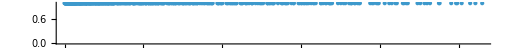

```mathematica
NumberLinePlot[simpalgrg]
```

### Properties and Relations

If all numeric leaves of an algebraic expression are equal to 1 or -1, LeafComplexity[expr] has the same value as LeafCount[expr]+1:

```mathematica
LeafComplexity[(x+1)/(x-1)+1/x]
```

14

```mathematica
LeafCount[(x+1)/(x-1)+1/x]+1
```

14

If no 0 appears in the expression, LeafComplexity[expr] is greater than LeafCount[expr]+1:

```mathematica
LeafComplexity[(2x+1)/(Sqrt[x]-1)+1/x]
```

22

```mathematica
LeafCount[(2x+1)/(Sqrt[x]-1)+1/x]+1
```

20

If 0s are present in the expression, LeafComplexity[expr] can be less than LeafCount[expr]+1:

```mathematica
LeafComplexity[{1,0,0,0}]
```

3

```mathematica
LeafCount[{1,0,0,0}]+1
```

6

If Infinity appears anywhere in the expression and does evaluate to 0, infinite is also the value of LeafComplexity:

```mathematica
LeafComplexity[x+1/Infinity]
```

2

```mathematica
LeafComplexity[x+Infinity]
```

∞

LeafComplexity[expr] can be also computed in terms of Cases as follows:

```mathematica
casesLC[expr_]:=
1+Total[Abs/@Flatten@Map[Cases[#//.{_Symbol?(!NumericQ[#]&)->1,c_Complex:>ReIm[c],r_Rational:>NumeratorDenominator[r]},_?NumericQ,{0,Infinity},Heads->True]&,Cases[expr,_?(NumericQ[#]&&AtomQ[#]&)|_Symbol?(!NumericQ[#]&),{0,Infinity},Heads->True]]]
```

```mathematica
expr=(2x^(1/3)+I)/(x-2-3I)- 5/x^2;
```

```mathematica
LeafComplexity[expr]//RepeatedTiming
```

{0.0000606722,36}

```mathematica
casesLC[expr]//RepeatedTiming
```

{0.000179614,36}

Notice though this is more involved and less efficient than the actual recursive definition.

### Neat Examples

Define a general LeafComplexity with doubly nested Log and Exp:

```mathematica
log2Exp2Complexity[range_]:=LeafComplexity[range,Log[1-Log[1-#]]&,Exp[#1-Exp[#2]]&]
```

Applying this to Range[n] for a few natural numbers n shows no Overflow and some interesting symbolic and numeric pattern:

```mathematica
Table[
With[{expr=Range[n]},
{llec=log2Exp2Complexity[expr]},
{n,N@llec,llec}],{n,1,12}]~Prepend~{"n","N[Log2Exp2Complexity[Range[n]]","Log2Exp2Complexity[Range[n]]"}//TableForm
```

n | N[Log2Exp2Complexity[Range[n]] | Log2Exp2Complexity[Range[n]]
1 | 0. | 0
2 | -0.367879 | -1/ⅇ
3 | -0.509293 | -2 ⅇ^(-1-1/ⅇ)
4 | -0.663199 | -3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ))
5 | -0.758127 | -4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ)))
6 | -0.861837 | -5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ))))
7 | -0.932321 | -6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ)))))
8 | -1.01368 | -7 ⅇ^(-1-6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ))))))
9 | -1.06797 | -8 ⅇ^(-1-7 ⅇ^(-1-6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ)))))))
10 | -1.13798 | -9 ⅇ^(-1-8 ⅇ^(-1-7 ⅇ^(-1-6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ))))))))
11 | -1.17893 | -10 ⅇ^(-1-9 ⅇ^(-1-8 ⅇ^(-1-7 ⅇ^(-1-6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ)))))))))
12 | -1.24479 | -11 ⅇ^(-1-10 ⅇ^(-1-9 ⅇ^(-1-8 ⅇ^(-1-7 ⅇ^(-1-6 ⅇ^(-1-5 ⅇ^(-1-4 ⅇ^(-1-3 ⅇ^(-1-2 ⅇ^(-1-1/ⅇ))))))))))

## Source & Additional Information

### Contributed By

Daniele Gregori

### Keywords

complexity

measure

function

tree

leaf

leaves

total

algebraic

expression

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

ComplexityFunction

LeafCount

AtomQ

FullForm

TreeForm

ExpressionTree

### Related Resource Objects

ProperLeafCount

DepthLeafCountSort

SKCombinatorLeftmostOutermostLeafCounts

AlgebraicRange

TranscendentalRange

FindClosedForm

### Source/Reference Citation

Source, reference or citation information

### Links

Integer Complexity | Wolfram Library Archive

### Tests

```mathematica
casesLC[expr_]:=
1+Total[Abs/@Flatten@Map[Cases[#//.{_Symbol?(!NumericQ[#]&)->1,c_Complex:>ReIm[c],r_Rational:>NumeratorDenominator[r]},_?NumericQ,{0,Infinity},Heads->True]&,Cases[expr,_?(NumericQ[#]&&AtomQ[#]&)|_Symbol?(!NumericQ[#]&),{0,Infinity},Heads->True]]]
```

```mathematica
testLC[expr_]:=
	VerificationTest[LeafComplexity[expr]//Echo,casesLC[expr]]
```

```mathematica
testLC[x+1]
```

4

TestObject[…]

```mathematica
testLC[x+10]
```

13

TestObject[…]

```mathematica
testLC[(x+2)/(y-2)]
```

12

TestObject[…]

```mathematica
testLC[(Sqrt[x]-1)/(y^(1/5)+2)]
```

24

TestObject[…]

```mathematica
testLC[(x+I)/(x-2-2I)- 4 I/x^2]
```

26

TestObject[…]

```mathematica
testLC[(2x^(1/3)+I)/(x-2-3I)- 5/x^2]
```

36

TestObject[…]

```mathematica
testLC[(-10-20a b^2-10a^2 b)/(a b)]
```

61

TestObject[…]

```mathematica
testLC[1.5 x^2+1.1 Log[y]]
```

12.6

TestObject[…]

```mathematica
testLC[E^x+Pi^2]
```

7+ⅇ+π

TestObject[…]

```mathematica
testLC[2 Log[a]+4 Log[-4]]
```

21+π

TestObject[…]

```mathematica
testLC[{1,2,{4,0,1,{0,6,3,4,{2,3,0},{5,2,0},1},0}}]
```

40

TestObject[…]

```mathematica
testLC[<|a->{2,3},b-><|{0,1}-><|γ->20,δ->40|>,{-1,-2}->50|>|>]
```

120

TestObject[…]

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

The design of this function benefited from suggestions by the Wolfram Review Team.

## Submission Notes

Additional information for the reviewer.